# 1 - D problem for ϵ(r)=∑e[G]ⅇ^(ⅈ G.r)

```mathematica
Element[{d,a,r,ϵa,ϵb},Reals]
```

(d|a|r|ϵa|ϵb)∈Reals

```mathematica
Element[{n,nn},Integers]
```

(n|nn)∈Integers

```mathematica
//Define Recipricol Lattic
```

```mathematica
b=2 π/d
```

(2 π)/d

```mathematica
// Define G
```

```mathematica
G[n_]=n b
```

(2 n π)/d

```mathematica
// Define ϵ
```

```mathematica
ϵ[r]=∑_G ϵr[G] ⅇ^(ⅈ G r)
```

```mathematica
ϵr[G]=1/A∫_cell ϵ[r] ⅇ^(-ⅈ G r)ⅆr
=(ϵa-ϵb)/A∫_0^a ⅇ^(-ⅈ G r)ⅆr+ϵb/A∫_0^d ⅇ^(-ⅈ G r)ⅆr
when G≠0, ∫_0^d ⅇ^(-ⅈ G r)ⅆr=0,ϵr[G]=S[G]=(ϵa-ϵb)/A∫_0^a ⅇ^(-ⅈ G r)ⅆr
when G=0,ϵr = (ϵa-ϵb)/A a+ϵb/A d=f ϵa+(1-f) ϵb=ϵbar, f=a/A
```

```mathematica
A=d
```

d

```mathematica
//for G≠0
```

```mathematica
S[n_]=(1/ϵa-1/ϵb)/A∫_0^a ⅇ^(-ⅈ G[n] r)ⅆr
```

-(ⅈ (1-ⅇ^(-(2 ⅈ a n π)/d)) (1/ϵa-1/ϵb))/(2 n π)

```mathematica
//for G=0
```

```mathematica
f=a/A
```

a/d

```mathematica
ϵbar=f  1/ϵa+(1-f) 1/ ϵb
```

a/(d ϵa)+(1-a/d)/ϵb

```mathematica
S[0]=ϵbar
```

a/(d ϵa)+(1-a/d)/ϵb

```mathematica
nn=5
```

5

```mathematica
ϵ[r_]=∑_(n=-nn)^nn S[n] ⅇ^(ⅈ G[n] r)
```

a/(d ϵa)-(ⅈ ⅇ^((2 ⅈ π r)/d) (1-ⅇ^(-(2 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(2 π)+(ⅈ ⅇ^(-(2 ⅈ π r)/d) (1-ⅇ^((2 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(2 π)-(ⅈ ⅇ^((4 ⅈ π r)/d) (1-ⅇ^(-(4 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(4 π)+(ⅈ ⅇ^(-(4 ⅈ π r)/d) (1-ⅇ^((4 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(4 π)-(ⅈ ⅇ^((6 ⅈ π r)/d) (1-ⅇ^(-(6 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(6 π)+(ⅈ ⅇ^(-(6 ⅈ π r)/d) (1-ⅇ^((6 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(6 π)-(ⅈ ⅇ^((8 ⅈ π r)/d) (1-ⅇ^(-(8 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(8 π)+(ⅈ ⅇ^(-(8 ⅈ π r)/d) (1-ⅇ^((8 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(8 π)-(ⅈ ⅇ^((10 ⅈ π r)/d) (1-ⅇ^(-(10 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(10 π)+(ⅈ ⅇ^(-(10 ⅈ π r)/d) (1-ⅇ^((10 ⅈ a π)/d)) (1/ϵa-1/ϵb))/(10 π)+(1-a/d)/ϵb

```mathematica
a=0.2;d=1;ϵa=10;ϵb=1
```

1

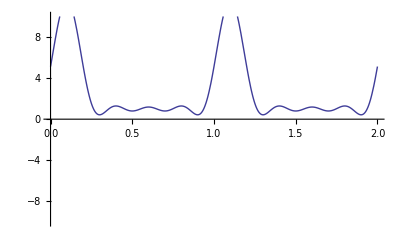

```mathematica
Plot[Re[ϵ[x]],{x,0,2},PlotRange->10]
```